```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

3.54491

0.403315

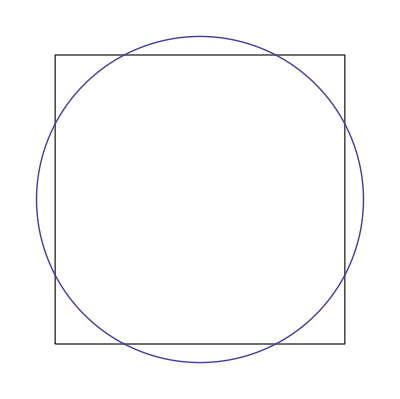

```mathematica
Clear[kF]
kF = N[ 2 Sqrt[Pi]] 
N[ 2 Sqrt[Pi] - Pi]  

Clear[p]
p = Module[{range, p, u, pp},
range = {-4, 4} ;
p = Pi/2 ;
u = {{0, p}, {p, 0}} ;
pp = ParametricPlot[ 
kF{Cos[t], Sin[t]}
, {t, 0, 2 Pi}
, PlotRange -> {range, range}
] ;
Show[Graphics[{
EdgeForm[Black],White,
Polygon[{{-Pi,-Pi},{-Pi,Pi},{Pi,Pi},{Pi,-Pi}}]
}]
,pp
]
]
```

```mathematica
peeters`exportForLatex["qmSolidsPs9P1bFig1", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs9P1bFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs9P1bFig1pn.png}